```mathematica
<<xlr8r.m
```

xCellerator 0.90 (26-Oct-2012) loaded Fri 2 Nov 2012 13:17:50
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

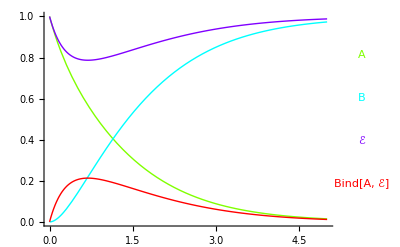

```mathematica
model={{Overscript[A⇄B, ℰ],a,d,k}};
sim=run[model,
"TimeSpan"-> 5,
"IC"-> {A-> 1,B-> 0,ℰ-> 1}, 
"Parameters"-> {a-> 1, d-> .1, k-> 2}];
runPlot[sim]
```

## Example with Boundary Conditions

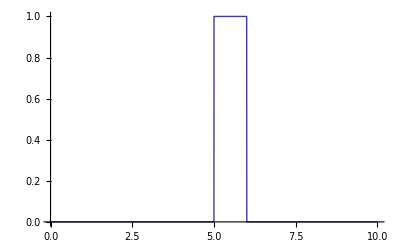

```mathematica
f[t_]:=Which[t<5,0,t<6,1,t>6,0];
Plot[f[t],{t,0,10}]
```

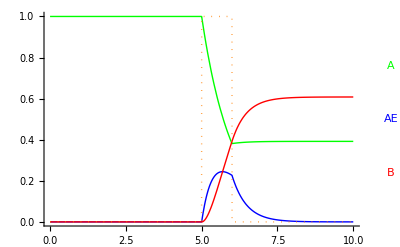

```mathematica
model={
{A+ℰ-> AE,a}, 
{AE-> A+ℰ, d}, 
{AE->  B+ℰ, k}};
sim=run[model,
"TimeSpan"-> 10,
"IC"-> {A-> 1,B-> 0}, 
"Parameters"-> {a-> 1, d-> .1, k-> 2},
"BoundaryConditions"->{ℰ[t]->f[t]}];
Show[
runPlot[sim],
Plot[f[t],{t,0,10}, 
PlotStyle-> {Orange, Dotted}]]
```